```mathematica
s=NDSolve[{y'[x]==y[x] Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
s=NDSolve[{y'[x]== 5 ,y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

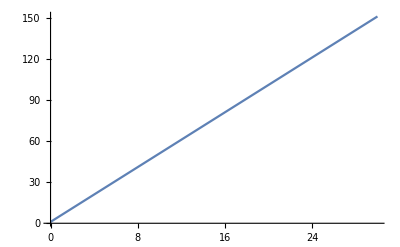

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

```mathematica
sol=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t],x[0]==y[0]==1},{x,y},{t,10}]
```

```mathematica
{{x->InterpolatingFunction[{{0., 10.}}, <>],y->InterpolatingFunction[{{0., 10.}}, <>]}}Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

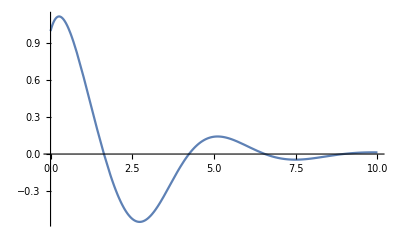

```mathematica
Plot[Evaluate[y[t]/.sol],{t,0,10},PlotRange->All]
```

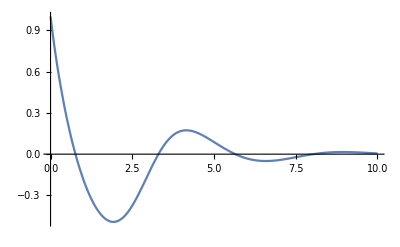

```mathematica
Plot[Evaluate[x[t]/.sol],{t,0,10},PlotRange->All]
```

```mathematica
Plot[Evaluate[y[t]/.sol],Evaluate[x[t]/.sol]{t,0,10},PlotRange->All]
```

Plot::pllim: Range specification Evaluate[x[t]/.sol] {t,0,10} is not of the form {x, xmin, xmax}.

Plot[{InterpolatingFunction[{{0., 10.}}, <>][t]},Evaluate[x[t]/.sol] {t,0,10},PlotRange→All]

```mathematica
clear
```

clear

```mathematica
sol=NDSolve[{x'[t]==-0.8y[t]-0.55x[t],y'[t]==0.8 x[t]-0.35y[t],x[0]==y[0]==0.1},{x,y},{t,10}]
```

{{x→InterpolatingFunction[{{0., 10.}}, <>],y→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

-Graphics-